### Imports

```mathematica
(* kill everything *)
ClearAll["Global`*"]
Remove["Global`*"]
```

```mathematica
SetDirectory["C:\\Users\\Tal Miller\\Dropbox\\UNI\\Courses Graduate\\QFT\\Papers and Reviews\\Supersymmetric index and Localization\\Thesis\\Notebooks\\Star_shaped_quivers"];
```

```mathematica
<<"CharactersFunctions.m"
```

LieART 1.1.5

last revised 7 August 2014

Needs::nocont: Context LieART`BranchingRules` was not created when Needs was evaluated.

```mathematica
Get["C:\\Program Files\\Wolfram Research\\Mathematica\\11.0\\AddOns\\Applications\\LieART\\LieART.m"]
```

LieART 1.1.5

last revised 7 August 2014

Needs::nocont: Context LieART`BranchingRules` was not created when Needs was evaluated.

```mathematica
maxVarNum=6;
a=Table[Subscript["a",i],{i,maxVarNum}];
b=Table[Subscript["b",i],{i,maxVarNum}];
$Assumptions={r>0,r<1};
```

### SO(7) chars

#### Rep {1,0,0}

```mathematica
algebraClass=B;
repDynkinLabels={1,0,0};
rank=Length[repDynkinLabels];
dynkinToIrrep[repDynkinLabels,algebraClass]
char=   dynkinToChar[a,repDynkinLabels,algebraClass]
```

7

a_1+a_2+a_3+1/a_2+1/a_3+1/a_1+1

```mathematica
expr=haarMeasure[a,algebraClass,rank,type->"Short"] *charToHilbertIntegrand[a,r,char,rank]
```

((1-a_1) (1-a_1/a_2) (1-a_2) (1-a_1 a_2) (1-a_1/a_3) (1-a_2/a_3) (1-a_3) (1-a_1 a_3) (1-a_2 a_3))/(a_1 a_2 a_3 (1-r) (1-r/a_1) (1-a_1 r) (1-r/a_2) (1-a_2 r) (1-r/a_3) (1-a_3 r))

```mathematica
{calcTime,hilbertComponents}=calcHilbertIntegral[a,r,expr,1,rank,0,"Branches"]//Timing;
Print["calculation time = ", calcTime, " seconds = ", calcTime/60^2, " hours"];
```

Level = 1

Number of relevant poles = 2

Calculating residue for pole 1/2 in level 1

Calculating residue for pole 2/2 in level 1

Residue for pole 1/2 in level 1 is non-zero, sending to level 2

Level = 2

Number of relevant poles = 1

Calculating residue for pole 1/1 in level 2

Residue for pole 1/1 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 1

Calculating residue for pole 1/1 in level 3

Residue for pole 2/2 in level 1 is zero.

calculation time = 0.15625 seconds = 0.0000434028 hours

```mathematica
hilbertFull=hilbertComponents//Flatten//Total//FullSimplify
```

1/(1-r^2)

Numeric divergence degree is -0.998006

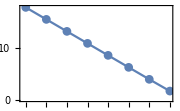

```mathematica
calcNumericDivergence[hilbertComponents]
```

#### Rep {1,0,0} + Rep {1,0,0}

```mathematica
algebraClass=B;
repDynkinLabels={1,0,0};
rank=Length[repDynkinLabels];
dynkinToIrrep[repDynkinLabels,algebraClass]
char= dynkinToChar[a,repDynkinLabels,algebraClass]
```

7

a_1+a_2+a_3+1/a_2+1/a_3+1/a_1+1

```mathematica
expr=haarMeasure[a,algebraClass,rank,type->"Short"] *charToHilbertIntegrand[a,r,2*char,rank]
```

((1-a_1) (1-a_1/a_2) (1-a_2) (1-a_1 a_2) (1-a_1/a_3) (1-a_2/a_3) (1-a_3) (1-a_1 a_3) (1-a_2 a_3))/(a_1 a_2 a_3 (1-r)^2 (1-r/a_1)^2 (1-a_1 r)^2 (1-r/a_2)^2 (1-a_2 r)^2 (1-r/a_3)^2 (1-a_3 r)^2)

```mathematica
{calcTime,hilbertComponents}=calcHilbertIntegral[a,r,expr,1,rank,0,"Branches"]//Timing;
Print["calculation time = ", calcTime, " seconds = ", calcTime/60^2, " hours"];
```

Level = 1

Number of relevant poles = 2

Calculating residue for pole 1/2 in level 1

Calculating residue for pole 2/2 in level 1

Residue for pole 1/2 in level 1 is non-zero, sending to level 2

Level = 2

Number of relevant poles = 1

Calculating residue for pole 1/1 in level 2

Residue for pole 1/1 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 1

Calculating residue for pole 1/1 in level 3

Residue for pole 2/2 in level 1 is zero.

calculation time = 0.234375 seconds = 0.0000651042 hours

```mathematica
hilbertFull=hilbertComponents//Flatten//Total//FullSimplify
```

-1/((r^2-1)^3)

Numeric divergence degree is -2.99402

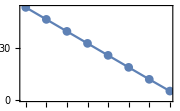

```mathematica
calcNumericDivergence[hilbertComponents]
```

#### Rep {0,0,1} (spin)

```mathematica
(* this is the spin representation, the character is given in terms of square roots which makes the calculation impossible with the same algorithm *)
```

```mathematica
algebraClass=B;
repDynkinLabels={0,0,1};
rank=Length[repDynkinLabels];
dynkinToIrrep[repDynkinLabels,algebraClass]
char=dynkinToChar[a,repDynkinLabels,algebraClass]
```

8

√a_2 √a_3 √a_1+(√a_3 √a_1)/(√a_2)+(√a_2 √a_1)/(√a_3)+(√a_1)/(√a_2 √a_3)+(√a_2 √a_3)/(√a_1)+(√a_3)/(√a_2 √a_1)+(√a_2)/(√a_3 √a_1)+1/(√a_2 √a_3 √a_1)

```mathematica
expr=haarMeasure[a,algebraClass,rank,type->"Short"] *charToHilbertIntegrand[a,r,char,rank]
```

((1-a_1) (1-a_1/a_2) (1-a_2) (1-a_1 a_2) (1-a_1/a_3) (1-a_2/a_3) (1-a_3) (1-a_1 a_3) (1-a_2 a_3))/(a_1 a_2 a_3 (1-r/(√a_1 √a_2 √a_3)) (1-(√a_1 r)/(√a_2 √a_3)) (1-(√a_2 r)/(√a_1 √a_3)) (1-(√a_1 √a_2 r)/(√a_3)) (1-(√a_3 r)/(√a_1 √a_2)) (1-(√a_1 √a_3 r)/(√a_2)) (1-(√a_2 √a_3 r)/(√a_1)) (1-√a_1 √a_2 √a_3 r))

```mathematica
{calcTime,hilbertComponents}=calcHilbertIntegral[a,r,expr,1,rank,0,"Simplify"]//Timing;
Print["calculation time = ", calcTime, " seconds = ", calcTime/60^2, " hours"];
```

Level = 1

Number of relevant poles = 5

Calculating residue for pole 1/5 in level 1

Residue calculation failed.

Failed residue exists in level 1, return "failed" flag

calculation time = 0.140625 seconds = 0.0000390625 hours

#### Rep {0,1,0} (adjoint)

```mathematica
algebraClass=B;
repDynkinLabels={0,1,0};
rank=Length[repDynkinLabels];
dynkinToIrrep[repDynkinLabels,algebraClass]
char=dynkinToChar[a,repDynkinLabels,algebraClass]
```

21

a_2 a_1+a_3 a_1+a_1/a_2+a_1/a_3+a_1+a_2+a_2 a_3+a_3/a_2+a_3+1/a_2+a_2/a_3+1/(a_2 a_3)+1/a_3+a_2/a_1+a_3/a_1+1/(a_2 a_1)+1/(a_3 a_1)+1/a_1+3

```mathematica
expr=haarMeasure[a,algebraClass,rank,type->"Short"] *charToHilbertIntegrand[a,r,char,rank]
```

((1-a_1) (1-a_1/a_2) (1-a_2) (1-a_1 a_2) (1-a_1/a_3) (1-a_2/a_3) (1-a_3) (1-a_1 a_3) (1-a_2 a_3))/(a_1 a_2 a_3 (1-r)^3 (1-r/a_1) (1-a_1 r) (1-r/a_2) (1-r/(a_1 a_2)) (1-(a_1 r)/a_2) (1-a_2 r) (1-(a_2 r)/a_1) (1-a_1 a_2 r) (1-r/a_3) (1-r/(a_1 a_3)) (1-(a_1 r)/a_3) (1-r/(a_2 a_3)) (1-(a_2 r)/a_3) (1-a_3 r) (1-(a_3 r)/a_1) (1-a_1 a_3 r) (1-(a_3 r)/a_2) (1-a_2 a_3 r))

```mathematica
{calcTime,hilbertComponents}=calcHilbertIntegral[a,r,expr,1,rank,0,"Branches"]//Timing;
Print["calculation time = ", calcTime, " seconds = ", calcTime/60^2, " hours"];
```

Level = 1

Number of relevant poles = 6

Calculating residue for pole 1/6 in level 1

Calculating residue for pole 2/6 in level 1

Calculating residue for pole 3/6 in level 1

Calculating residue for pole 4/6 in level 1

Calculating residue for pole 5/6 in level 1

Calculating residue for pole 6/6 in level 1

Residue for pole 1/6 in level 1 is non-zero, sending to level 2

Level = 2

Number of relevant poles = 3

Calculating residue for pole 1/3 in level 2

Calculating residue for pole 2/3 in level 2

Calculating residue for pole 3/3 in level 2

Residue for pole 1/3 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 2

Calculating residue for pole 1/2 in level 3

Calculating residue for pole 2/2 in level 3

Residue for pole 2/3 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 2

Calculating residue for pole 1/2 in level 3

Calculating residue for pole 2/2 in level 3

Residue for pole 3/3 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 4

Calculating residue for pole 1/4 in level 3

Calculating residue for pole 2/4 in level 3

Calculating residue for pole 3/4 in level 3

Calculating residue for pole 4/4 in level 3

Residue for pole 2/6 in level 1 is zero.

Residue for pole 3/6 in level 1 is non-zero, sending to level 2

Level = 2

Number of relevant poles = 5

Calculating residue for pole 1/5 in level 2

Calculating residue for pole 2/5 in level 2

Calculating residue for pole 3/5 in level 2

Calculating residue for pole 4/5 in level 2

Calculating residue for pole 5/5 in level 2

Residue for pole 1/5 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 2

Calculating residue for pole 1/2 in level 3

Calculating residue for pole 2/2 in level 3

Residue for pole 2/5 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 3

Calculating residue for pole 1/3 in level 3

Calculating residue for pole 2/3 in level 3

Calculating residue for pole 3/3 in level 3

Residue for pole 3/5 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 2

Calculating residue for pole 1/2 in level 3

Calculating residue for pole 2/2 in level 3

Residue for pole 4/5 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 1

Calculating residue for pole 1/1 in level 3

Residue for pole 5/5 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 5

Calculating residue for pole 1/5 in level 3

Calculating residue for pole 2/5 in level 3

Calculating residue for pole 3/5 in level 3

Calculating residue for pole 4/5 in level 3

Calculating residue for pole 5/5 in level 3

Residue for pole 4/6 in level 1 is non-zero, sending to level 2

Level = 2

Number of relevant poles = 3

Calculating residue for pole 1/3 in level 2

Calculating residue for pole 2/3 in level 2

Calculating residue for pole 3/3 in level 2

Residue for pole 1/3 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 2

Calculating residue for pole 1/2 in level 3

Calculating residue for pole 2/2 in level 3

Residue for pole 2/3 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 1

Calculating residue for pole 1/1 in level 3

Residue for pole 3/3 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 5

Calculating residue for pole 1/5 in level 3

Calculating residue for pole 2/5 in level 3

Calculating residue for pole 3/5 in level 3

Calculating residue for pole 4/5 in level 3

Calculating residue for pole 5/5 in level 3

Residue for pole 5/6 in level 1 is non-zero, sending to level 2

Level = 2

Number of relevant poles = 3

Calculating residue for pole 1/3 in level 2

Calculating residue for pole 2/3 in level 2

Calculating residue for pole 3/3 in level 2

Residue for pole 1/3 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 4

Calculating residue for pole 1/4 in level 3

Calculating residue for pole 2/4 in level 3

Calculating residue for pole 3/4 in level 3

Calculating residue for pole 4/4 in level 3

Residue for pole 2/3 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 3

Calculating residue for pole 1/3 in level 3

Calculating residue for pole 2/3 in level 3

Calculating residue for pole 3/3 in level 3

Residue for pole 3/3 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 5

Calculating residue for pole 1/5 in level 3

Calculating residue for pole 2/5 in level 3

Calculating residue for pole 3/5 in level 3

Calculating residue for pole 4/5 in level 3

Calculating residue for pole 5/5 in level 3

Residue for pole 6/6 in level 1 is non-zero, sending to level 2

Level = 2

Number of relevant poles = 3

Calculating residue for pole 1/3 in level 2

Calculating residue for pole 2/3 in level 2

Calculating residue for pole 3/3 in level 2

Residue for pole 1/3 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 2

Calculating residue for pole 1/2 in level 3

Calculating residue for pole 2/2 in level 3

Residue for pole 2/3 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 1

Calculating residue for pole 1/1 in level 3

Residue for pole 3/3 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 3

Calculating residue for pole 1/3 in level 3

Calculating residue for pole 2/3 in level 3

Calculating residue for pole 3/3 in level 3

calculation time = 5.125 seconds = 0.00142361 hours

```mathematica
hilbertFull=hilbertComponents//Flatten//Total//FullSimplify
```

-1/((r^2-1)^3 (r^6+2 r^4+2 r^2+1))

Numeric divergence degree is -2.98249

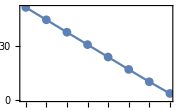

```mathematica
calcNumericDivergence[hilbertComponents]
```

#### Rep {2,0,0}

```mathematica
algebraClass=B;
repDynkinLabels={2,0,0};
rank=Length[repDynkinLabels];
dynkinToIrrep[repDynkinLabels,algebraClass]
char=dynkinToChar[a,repDynkinLabels,algebraClass]
```

27

a_1^2+a_2 a_1+a_3 a_1+a_1/a_2+a_1/a_3+a_1+a_2^2+a_3^2+a_2+a_2 a_3+a_3/a_2+a_3+1/a_2+a_2/a_3+1/(a_2 a_3)+1/a_3+1/a_2^2+1/a_3^2+a_2/a_1+a_3/a_1+1/(a_2 a_1)+1/(a_3 a_1)+1/a_1+1/a_1^2+3

```mathematica
expr=haarMeasure[a,algebraClass,rank,type->"Short"] *charToHilbertIntegrand[a,r,char,rank]
```

((1-a_1) (1-a_1/a_2) (1-a_2) (1-a_1 a_2) (1-a_1/a_3) (1-a_2/a_3) (1-a_3) (1-a_1 a_3) (1-a_2 a_3))/(a_1 a_2 a_3 (1-r)^3 (1-r/a_1^2) (1-r/a_1) (1-a_1 r) (1-a_1^2 r) (1-r/a_2^2) (1-r/a_2) (1-r/(a_1 a_2)) (1-(a_1 r)/a_2) (1-a_2 r) (1-(a_2 r)/a_1) (1-a_1 a_2 r) (1-a_2^2 r) (1-r/a_3^2) (1-r/a_3) (1-r/(a_1 a_3)) (1-(a_1 r)/a_3) (1-r/(a_2 a_3)) (1-(a_2 r)/a_3) (1-a_3 r) (1-(a_3 r)/a_1) (1-a_1 a_3 r) (1-(a_3 r)/a_2) (1-a_2 a_3 r) (1-a_3^2 r))

```mathematica
{calcTime,hilbertComponents}=calcHilbertIntegral[a,r,expr,1,rank,0,"Branches"]//Timing;
Print["calculation time = ", calcTime, " seconds = ", calcTime/60^2, " hours"];
```

Level = 1

Number of relevant poles = 8

Calculating residue for pole 1/8 in level 1

Calculating residue for pole 2/8 in level 1

Calculating residue for pole 3/8 in level 1

Calculating residue for pole 4/8 in level 1

Calculating residue for pole 5/8 in level 1

Calculating residue for pole 6/8 in level 1

Calculating residue for pole 7/8 in level 1

Calculating residue for pole 8/8 in level 1

Residue for pole 1/8 in level 1 is non-zero, sending to level 2

Level = 2

Number of relevant poles = 6

Calculating residue for pole 1/6 in level 2

Calculating residue for pole 2/6 in level 2

Calculating residue for pole 3/6 in level 2

Calculating residue for pole 4/6 in level 2

Calculating residue for pole 5/6 in level 2

Calculating residue for pole 6/6 in level 2

Residue for pole 1/6 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 4

Calculating residue for pole 1/4 in level 3

Calculating residue for pole 2/4 in level 3

Calculating residue for pole 3/4 in level 3

Calculating residue for pole 4/4 in level 3

Residue for pole 2/6 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 4

Calculating residue for pole 1/4 in level 3

Calculating residue for pole 2/4 in level 3

Calculating residue for pole 3/4 in level 3

Calculating residue for pole 4/4 in level 3

Residue for pole 3/6 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 4

Calculating residue for pole 1/4 in level 3

Calculating residue for pole 2/4 in level 3

Calculating residue for pole 3/4 in level 3

Calculating residue for pole 4/4 in level 3

Residue for pole 4/6 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 5

Calculating residue for pole 1/5 in level 3

Calculating residue for pole 2/5 in level 3

Calculating residue for pole 3/5 in level 3

Calculating residue for pole 4/5 in level 3

Calculating residue for pole 5/5 in level 3

Residue for pole 5/6 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 4

Calculating residue for pole 1/4 in level 3

Calculating residue for pole 2/4 in level 3

Calculating residue for pole 3/4 in level 3

Calculating residue for pole 4/4 in level 3

Residue for pole 6/6 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 8

Calculating residue for pole 1/8 in level 3

Calculating residue for pole 2/8 in level 3

Calculating residue for pole 3/8 in level 3

Calculating residue for pole 4/8 in level 3

Calculating residue for pole 5/8 in level 3

Calculating residue for pole 6/8 in level 3

Calculating residue for pole 7/8 in level 3

Calculating residue for pole 8/8 in level 3

Residue for pole 2/8 in level 1 is non-zero, sending to level 2

Level = 2

Number of relevant poles = 6

Calculating residue for pole 1/6 in level 2

Calculating residue for pole 2/6 in level 2

Calculating residue for pole 3/6 in level 2

Calculating residue for pole 4/6 in level 2

Calculating residue for pole 5/6 in level 2

Calculating residue for pole 6/6 in level 2

Residue for pole 1/6 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 4

Calculating residue for pole 1/4 in level 3

Calculating residue for pole 2/4 in level 3

Calculating residue for pole 3/4 in level 3

Calculating residue for pole 4/4 in level 3

Residue for pole 2/6 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 4

Calculating residue for pole 1/4 in level 3

Calculating residue for pole 2/4 in level 3

Calculating residue for pole 3/4 in level 3

Calculating residue for pole 4/4 in level 3

Residue for pole 3/6 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 5

Calculating residue for pole 1/5 in level 3

Calculating residue for pole 2/5 in level 3

Calculating residue for pole 3/5 in level 3

Calculating residue for pole 4/5 in level 3

Calculating residue for pole 5/5 in level 3

Residue for pole 4/6 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 4

Calculating residue for pole 1/4 in level 3

Calculating residue for pole 2/4 in level 3

Calculating residue for pole 3/4 in level 3

Calculating residue for pole 4/4 in level 3

Residue for pole 5/6 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 4

Calculating residue for pole 1/4 in level 3

Calculating residue for pole 2/4 in level 3

Calculating residue for pole 3/4 in level 3

Calculating residue for pole 4/4 in level 3

Residue for pole 6/6 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 8

Calculating residue for pole 1/8 in level 3

Calculating residue for pole 2/8 in level 3

Calculating residue for pole 3/8 in level 3

Calculating residue for pole 4/8 in level 3

Calculating residue for pole 5/8 in level 3

Calculating residue for pole 6/8 in level 3

Calculating residue for pole 7/8 in level 3

Calculating residue for pole 8/8 in level 3

Residue for pole 3/8 in level 1 is non-zero, sending to level 2

Level = 2

Number of relevant poles = 5

Calculating residue for pole 1/5 in level 2

Calculating residue for pole 2/5 in level 2

Calculating residue for pole 3/5 in level 2

Calculating residue for pole 4/5 in level 2

Calculating residue for pole 5/5 in level 2

Residue for pole 1/5 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 4

Calculating residue for pole 1/4 in level 3

Calculating residue for pole 2/4 in level 3

Calculating residue for pole 3/4 in level 3

Calculating residue for pole 4/4 in level 3

Residue for pole 2/5 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 4

Calculating residue for pole 1/4 in level 3

Calculating residue for pole 2/4 in level 3

Calculating residue for pole 3/4 in level 3

Calculating residue for pole 4/4 in level 3

Residue for pole 3/5 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 4

Calculating residue for pole 1/4 in level 3

Calculating residue for pole 2/4 in level 3

Calculating residue for pole 3/4 in level 3

Calculating residue for pole 4/4 in level 3

Residue for pole 4/5 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 4

Calculating residue for pole 1/4 in level 3

Calculating residue for pole 2/4 in level 3

Calculating residue for pole 3/4 in level 3

Calculating residue for pole 4/4 in level 3

Residue for pole 5/5 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 8

Calculating residue for pole 1/8 in level 3

Calculating residue for pole 2/8 in level 3

Calculating residue for pole 3/8 in level 3

Calculating residue for pole 4/8 in level 3

Calculating residue for pole 5/8 in level 3

Calculating residue for pole 6/8 in level 3

Calculating residue for pole 7/8 in level 3

Calculating residue for pole 8/8 in level 3

Residue for pole 4/8 in level 1 is zero.

Residue for pole 5/8 in level 1 is non-zero, sending to level 2

Level = 2

Number of relevant poles = 9

Calculating residue for pole 1/9 in level 2

Calculating residue for pole 2/9 in level 2

Calculating residue for pole 3/9 in level 2

Calculating residue for pole 4/9 in level 2

Calculating residue for pole 5/9 in level 2

Calculating residue for pole 6/9 in level 2

Calculating residue for pole 7/9 in level 2

Calculating residue for pole 8/9 in level 2

Calculating residue for pole 9/9 in level 2

Residue for pole 1/9 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 4

Calculating residue for pole 1/4 in level 3

Calculating residue for pole 2/4 in level 3

Calculating residue for pole 3/4 in level 3

Calculating residue for pole 4/4 in level 3

Residue for pole 2/9 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 4

Calculating residue for pole 1/4 in level 3

Calculating residue for pole 2/4 in level 3

Calculating residue for pole 3/4 in level 3

Calculating residue for pole 4/4 in level 3

Residue for pole 3/9 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 4

Calculating residue for pole 1/4 in level 3

Calculating residue for pole 2/4 in level 3

Calculating residue for pole 3/4 in level 3

Calculating residue for pole 4/4 in level 3

Residue for pole 4/9 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 5

Calculating residue for pole 1/5 in level 3

Calculating residue for pole 2/5 in level 3

Calculating residue for pole 3/5 in level 3

Calculating residue for pole 4/5 in level 3

Calculating residue for pole 5/5 in level 3

Residue for pole 5/9 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 4

Calculating residue for pole 1/4 in level 3

Calculating residue for pole 2/4 in level 3

Calculating residue for pole 3/4 in level 3

Calculating residue for pole 4/4 in level 3

Residue for pole 6/9 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 4

Calculating residue for pole 1/4 in level 3

Calculating residue for pole 2/4 in level 3

Calculating residue for pole 3/4 in level 3

Calculating residue for pole 4/4 in level 3

Residue for pole 7/9 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 4

Calculating residue for pole 1/4 in level 3

Calculating residue for pole 2/4 in level 3

Calculating residue for pole 3/4 in level 3

Calculating residue for pole 4/4 in level 3

Residue for pole 8/9 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 3

Calculating residue for pole 1/3 in level 3

Calculating residue for pole 2/3 in level 3

Calculating residue for pole 3/3 in level 3

Residue for pole 9/9 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 11

Calculating residue for pole 1/11 in level 3

Calculating residue for pole 2/11 in level 3

Calculating residue for pole 3/11 in level 3

Calculating residue for pole 4/11 in level 3

Calculating residue for pole 5/11 in level 3

Calculating residue for pole 6/11 in level 3

Calculating residue for pole 7/11 in level 3

Calculating residue for pole 8/11 in level 3

Calculating residue for pole 9/11 in level 3

Calculating residue for pole 10/11 in level 3

Calculating residue for pole 11/11 in level 3

Residue for pole 6/8 in level 1 is non-zero, sending to level 2

Level = 2

Number of relevant poles = 5

Calculating residue for pole 1/5 in level 2

Calculating residue for pole 2/5 in level 2

Calculating residue for pole 3/5 in level 2

Calculating residue for pole 4/5 in level 2

Calculating residue for pole 5/5 in level 2

Residue for pole 1/5 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 4

Calculating residue for pole 1/4 in level 3

Calculating residue for pole 2/4 in level 3

Calculating residue for pole 3/4 in level 3

Calculating residue for pole 4/4 in level 3

Residue for pole 2/5 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 4

Calculating residue for pole 1/4 in level 3

Calculating residue for pole 2/4 in level 3

Calculating residue for pole 3/4 in level 3

Calculating residue for pole 4/4 in level 3

Residue for pole 3/5 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 4

Calculating residue for pole 1/4 in level 3

Calculating residue for pole 2/4 in level 3

Calculating residue for pole 3/4 in level 3

Calculating residue for pole 4/4 in level 3

Residue for pole 4/5 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 3

Calculating residue for pole 1/3 in level 3

Calculating residue for pole 2/3 in level 3

Calculating residue for pole 3/3 in level 3

Residue for pole 5/5 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 11

Calculating residue for pole 1/11 in level 3

Calculating residue for pole 2/11 in level 3

Calculating residue for pole 3/11 in level 3

Calculating residue for pole 4/11 in level 3

Calculating residue for pole 5/11 in level 3

Calculating residue for pole 6/11 in level 3

Calculating residue for pole 7/11 in level 3

Calculating residue for pole 8/11 in level 3

Calculating residue for pole 9/11 in level 3

Calculating residue for pole 10/11 in level 3

Calculating residue for pole 11/11 in level 3

Residue for pole 7/8 in level 1 is non-zero, sending to level 2

Level = 2

Number of relevant poles = 5

Calculating residue for pole 1/5 in level 2

Calculating residue for pole 2/5 in level 2

Calculating residue for pole 3/5 in level 2

Calculating residue for pole 4/5 in level 2

Calculating residue for pole 5/5 in level 2

Residue for pole 1/5 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 8

Calculating residue for pole 1/8 in level 3

Calculating residue for pole 2/8 in level 3

Calculating residue for pole 3/8 in level 3

Calculating residue for pole 4/8 in level 3

Calculating residue for pole 5/8 in level 3

Calculating residue for pole 6/8 in level 3

Calculating residue for pole 7/8 in level 3

Calculating residue for pole 8/8 in level 3

Residue for pole 2/5 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 8

Calculating residue for pole 1/8 in level 3

Calculating residue for pole 2/8 in level 3

Calculating residue for pole 3/8 in level 3

Calculating residue for pole 4/8 in level 3

Calculating residue for pole 5/8 in level 3

Calculating residue for pole 6/8 in level 3

Calculating residue for pole 7/8 in level 3

Calculating residue for pole 8/8 in level 3

Residue for pole 3/5 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 8

Calculating residue for pole 1/8 in level 3

Calculating residue for pole 2/8 in level 3

Calculating residue for pole 3/8 in level 3

Calculating residue for pole 4/8 in level 3

Calculating residue for pole 5/8 in level 3

Calculating residue for pole 6/8 in level 3

Calculating residue for pole 7/8 in level 3

Calculating residue for pole 8/8 in level 3

Residue for pole 4/5 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 7

Calculating residue for pole 1/7 in level 3

Calculating residue for pole 2/7 in level 3

Calculating residue for pole 3/7 in level 3

Calculating residue for pole 4/7 in level 3

Calculating residue for pole 5/7 in level 3

Calculating residue for pole 6/7 in level 3

Calculating residue for pole 7/7 in level 3

Residue for pole 5/5 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 11

Calculating residue for pole 1/11 in level 3

Calculating residue for pole 2/11 in level 3

Calculating residue for pole 3/11 in level 3

Calculating residue for pole 4/11 in level 3

Calculating residue for pole 5/11 in level 3

Calculating residue for pole 6/11 in level 3

Calculating residue for pole 7/11 in level 3

Calculating residue for pole 8/11 in level 3

Calculating residue for pole 9/11 in level 3

Calculating residue for pole 10/11 in level 3

Calculating residue for pole 11/11 in level 3

Residue for pole 8/8 in level 1 is non-zero, sending to level 2

Level = 2

Number of relevant poles = 5

Calculating residue for pole 1/5 in level 2

Calculating residue for pole 2/5 in level 2

Calculating residue for pole 3/5 in level 2

Calculating residue for pole 4/5 in level 2

Calculating residue for pole 5/5 in level 2

Residue for pole 1/5 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 4

Calculating residue for pole 1/4 in level 3

Calculating residue for pole 2/4 in level 3

Calculating residue for pole 3/4 in level 3

Calculating residue for pole 4/4 in level 3

Residue for pole 2/5 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 4

Calculating residue for pole 1/4 in level 3

Calculating residue for pole 2/4 in level 3

Calculating residue for pole 3/4 in level 3

Calculating residue for pole 4/4 in level 3

Residue for pole 3/5 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 4

Calculating residue for pole 1/4 in level 3

Calculating residue for pole 2/4 in level 3

Calculating residue for pole 3/4 in level 3

Calculating residue for pole 4/4 in level 3

Residue for pole 4/5 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 3

Calculating residue for pole 1/3 in level 3

Calculating residue for pole 2/3 in level 3

Calculating residue for pole 3/3 in level 3

Residue for pole 5/5 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 7

Calculating residue for pole 1/7 in level 3

Calculating residue for pole 2/7 in level 3

Calculating residue for pole 3/7 in level 3

Calculating residue for pole 4/7 in level 3

Calculating residue for pole 5/7 in level 3

Calculating residue for pole 6/7 in level 3

Calculating residue for pole 7/7 in level 3

calculation time = 24.9531 seconds = 0.00693142 hours

```mathematica
hilbertFull=hilbertComponents//Flatten//Total//FullSimplify
```

1/((r-1)^6 (r+1)^3 ((r-1) r+1) (r^2+1) (r^2+r+1)^2 (r^4+r^3+r^2+r+1) (r^6+r^5+r^4+r^3+r^2+r+1))

Numeric divergence degree is -5.9593

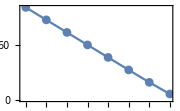

```mathematica
calcNumericDivergence[hilbertComponents]
```

### SO(7) + U(1) chars

#### SO(7) rep {1,0,0} + rep {1,0,0} with opposite U(1) charges

```mathematica
algebraClass=B;
repDynkinLabels={1,0,0};
rank=Length[repDynkinLabels];
dynkinToIrrep[repDynkinLabels,algebraClass]
char= dynkinToChar[a,repDynkinLabels,algebraClass]
```

7

a_1+a_2+a_3+1/a_2+1/a_3+1/a_1+1

```mathematica
cartanVars=Join[{t},a];
rankTot=Length[repDynkinLabels]+1;
haarU1=1/t;
```

```mathematica
expr=haarU1*haarMeasure[a,algebraClass,rank,type->"Short"] *charToHilbertIntegrand[cartanVars,r,t char+1/t char,rankTot]
```

((1-a_1) (1-a_1/a_2) (1-a_2) (1-a_1 a_2) (1-a_1/a_3) (1-a_2/a_3) (1-a_3) (1-a_1 a_3) (1-a_2 a_3))/(a_1 a_2 a_3 t (1-r/t) (1-r t) (1-r/(a_1 t)) (1-(r t)/a_1) (1-(a_1 r)/t) (1-a_1 r t) (1-r/(a_2 t)) (1-(r t)/a_2) (1-(a_2 r)/t) (1-a_2 r t) (1-r/(a_3 t)) (1-(r t)/a_3) (1-(a_3 r)/t) (1-a_3 r t))

```mathematica
{calcTime,hilbertComponents}=calcHilbertIntegral[cartanVars,r,expr,1,rankTot,0,"Branches"]//Timing;
Print["calculation time = ", calcTime, " seconds = ", calcTime/60^2, " hours"];
```

Level = 1

Number of relevant poles = 8

Calculating residue for pole 1/8 in level 1

Calculating residue for pole 2/8 in level 1

Calculating residue for pole 3/8 in level 1

Calculating residue for pole 4/8 in level 1

Calculating residue for pole 5/8 in level 1

Calculating residue for pole 6/8 in level 1

Calculating residue for pole 7/8 in level 1

Calculating residue for pole 8/8 in level 1

Residue for pole 1/8 in level 1 is non-zero, sending to level 2

Level = 2

Number of relevant poles = 1

Calculating residue for pole 1/1 in level 2

Residue for pole 1/1 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 0

Residue for pole 2/8 in level 1 is zero.

Residue for pole 3/8 in level 1 is non-zero, sending to level 2

Level = 2

Number of relevant poles = 7

Calculating residue for pole 1/7 in level 2

Calculating residue for pole 2/7 in level 2

Calculating residue for pole 3/7 in level 2

Calculating residue for pole 4/7 in level 2

Calculating residue for pole 5/7 in level 2

Calculating residue for pole 6/7 in level 2

Calculating residue for pole 7/7 in level 2

Residue for pole 1/7 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 0

Residue for pole 2/7 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 1

Calculating residue for pole 1/1 in level 3

Residue for pole 1/1 in level 3 is non-zero, sending to level 4

Level = 4

Number of relevant poles = 1

Calculating residue for pole 1/1 in level 4

Residue for pole 3/7 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 1

Calculating residue for pole 1/1 in level 3

Residue for pole 1/1 in level 3 is non-zero, sending to level 4

Level = 4

Number of relevant poles = 1

Calculating residue for pole 1/1 in level 4

Residue for pole 4/7 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 0

Residue for pole 5/7 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 4

Calculating residue for pole 1/4 in level 3

Calculating residue for pole 2/4 in level 3

Calculating residue for pole 3/4 in level 3

Calculating residue for pole 4/4 in level 3

Residue for pole 1/4 in level 3 is non-zero, sending to level 4

Level = 4

Number of relevant poles = 1

Calculating residue for pole 1/1 in level 4

Residue for pole 2/4 in level 3 is non-zero, sending to level 4

Level = 4

Number of relevant poles = 1

Calculating residue for pole 1/1 in level 4

Residue for pole 3/4 in level 3 is non-zero, sending to level 4

Level = 4

Number of relevant poles = 1

Calculating residue for pole 1/1 in level 4

Residue for pole 4/4 in level 3 is non-zero, sending to level 4

Level = 4

Number of relevant poles = 1

Calculating residue for pole 1/1 in level 4

Residue for pole 6/7 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 0

Residue for pole 7/7 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 0

Residue for pole 4/8 in level 1 is non-zero, sending to level 2

Level = 2

Number of relevant poles = 0

Residue for pole 5/8 in level 1 is non-zero, sending to level 2

Level = 2

Number of relevant poles = 1

Calculating residue for pole 1/1 in level 2

Residue for pole 1/1 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 4

Calculating residue for pole 1/4 in level 3

Calculating residue for pole 2/4 in level 3

Calculating residue for pole 3/4 in level 3

Calculating residue for pole 4/4 in level 3

Residue for pole 1/4 in level 3 is non-zero, sending to level 4

Level = 4

Number of relevant poles = 1

Calculating residue for pole 1/1 in level 4

Residue for pole 2/4 in level 3 is non-zero, sending to level 4

Level = 4

Number of relevant poles = 1

Calculating residue for pole 1/1 in level 4

Residue for pole 3/4 in level 3 is non-zero, sending to level 4

Level = 4

Number of relevant poles = 1

Calculating residue for pole 1/1 in level 4

Residue for pole 4/4 in level 3 is non-zero, sending to level 4

Level = 4

Number of relevant poles = 1

Calculating residue for pole 1/1 in level 4

Residue for pole 6/8 in level 1 is non-zero, sending to level 2

Level = 2

Number of relevant poles = 1

Calculating residue for pole 1/1 in level 2

Residue for pole 1/1 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 0

Residue for pole 7/8 in level 1 is non-zero, sending to level 2

Level = 2

Number of relevant poles = 1

Calculating residue for pole 1/1 in level 2

Residue for pole 1/1 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 0

Residue for pole 8/8 in level 1 is non-zero, sending to level 2

Level = 2

Number of relevant poles = 1

Calculating residue for pole 1/1 in level 2

Residue for pole 1/1 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 0

calculation time = 3.96875 seconds = 0.00110243 hours

```mathematica
hilbertComponents//Flatten//Total//Simplify
```

1/((r^2-1)^2 (r^2+1))

Numeric divergence degree is -1.99213

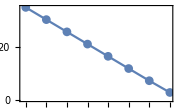

```mathematica
calcNumericDivergence[hilbertComponents]
```

#### SO(7) rep {0,1,0} + singlet with opposite U(1) charges

```mathematica
algebraClass=B;
repDynkinLabels={0,1,0};
rank=Length[repDynkinLabels];
dynkinToIrrep[repDynkinLabels,algebraClass]
char= dynkinToChar[a,repDynkinLabels,algebraClass]
```

21

a_2 a_1+a_3 a_1+a_1/a_2+a_1/a_3+a_1+a_2+a_2 a_3+a_3/a_2+a_3+1/a_2+a_2/a_3+1/(a_2 a_3)+1/a_3+a_2/a_1+a_3/a_1+1/(a_2 a_1)+1/(a_3 a_1)+1/a_1+3

```mathematica
cartanVars=Join[{t},a];
rankTot=Length[repDynkinLabels]+1;
haarU1=1/t;
```

```mathematica
expr=haarU1*haarMeasure[a,algebraClass,rank,type->"Short"] *charToHilbertIntegrand[cartanVars,r,t char+1/t,rankTot]
```

((1-a_1) (1-a_1/a_2) (1-a_2) (1-a_1 a_2) (1-a_1/a_3) (1-a_2/a_3) (1-a_3) (1-a_1 a_3) (1-a_2 a_3))/(a_1 a_2 a_3 t (1-r/t) (1-r t)^3 (1-(r t)/a_1) (1-a_1 r t) (1-(r t)/a_2) (1-(r t)/(a_1 a_2)) (1-(a_1 r t)/a_2) (1-a_2 r t) (1-(a_2 r t)/a_1) (1-a_1 a_2 r t) (1-(r t)/a_3) (1-(r t)/(a_1 a_3)) (1-(a_1 r t)/a_3) (1-(r t)/(a_2 a_3)) (1-(a_2 r t)/a_3) (1-a_3 r t) (1-(a_3 r t)/a_1) (1-a_1 a_3 r t) (1-(a_3 r t)/a_2) (1-a_2 a_3 r t))

```mathematica
{calcTime,hilbertComponents}=calcHilbertIntegral[cartanVars,r,expr,1,rankTot,0,"Branches"]//Timing;
Print["calculation time = ", calcTime, " seconds = ", calcTime/60^2, " hours"];
```

Level = 1

Number of relevant poles = 2

Calculating residue for pole 1/2 in level 1

Calculating residue for pole 2/2 in level 1

Residue for pole 1/2 in level 1 is non-zero, sending to level 2

Level = 2

Number of relevant poles = 5

Calculating residue for pole 1/5 in level 2

Calculating residue for pole 2/5 in level 2

Calculating residue for pole 3/5 in level 2

Calculating residue for pole 4/5 in level 2

Calculating residue for pole 5/5 in level 2

Residue for pole 1/5 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 3

Calculating residue for pole 1/3 in level 3

Calculating residue for pole 2/3 in level 3

Calculating residue for pole 3/3 in level 3

Residue for pole 1/3 in level 3 is non-zero, sending to level 4

Level = 4

Number of relevant poles = 2

Calculating residue for pole 1/2 in level 4

Calculating residue for pole 2/2 in level 4

Residue for pole 2/3 in level 3 is non-zero, sending to level 4

Level = 4

Number of relevant poles = 2

Calculating residue for pole 1/2 in level 4

Calculating residue for pole 2/2 in level 4

Residue for pole 3/3 in level 3 is non-zero, sending to level 4

Level = 4

Number of relevant poles = 4

Calculating residue for pole 1/4 in level 4

Calculating residue for pole 2/4 in level 4

Calculating residue for pole 3/4 in level 4

Calculating residue for pole 4/4 in level 4

Residue for pole 2/5 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 3

Calculating residue for pole 1/3 in level 3

Calculating residue for pole 2/3 in level 3

Calculating residue for pole 3/3 in level 3

Residue for pole 1/3 in level 3 is non-zero, sending to level 4

Level = 4

Number of relevant poles = 2

Calculating residue for pole 1/2 in level 4

Calculating residue for pole 2/2 in level 4

Residue for pole 2/3 in level 3 is non-zero, sending to level 4

Level = 4

Number of relevant poles = 1

Calculating residue for pole 1/1 in level 4

Residue for pole 3/3 in level 3 is non-zero, sending to level 4

Level = 4

Number of relevant poles = 5

Calculating residue for pole 1/5 in level 4

Calculating residue for pole 2/5 in level 4

Calculating residue for pole 3/5 in level 4

Calculating residue for pole 4/5 in level 4

Calculating residue for pole 5/5 in level 4

Residue for pole 3/5 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 5

Calculating residue for pole 1/5 in level 3

Calculating residue for pole 2/5 in level 3

Calculating residue for pole 3/5 in level 3

Calculating residue for pole 4/5 in level 3

Calculating residue for pole 5/5 in level 3

Residue for pole 1/5 in level 3 is non-zero, sending to level 4

Level = 4

Number of relevant poles = 2

Calculating residue for pole 1/2 in level 4

Calculating residue for pole 2/2 in level 4

Residue for pole 2/5 in level 3 is non-zero, sending to level 4

Level = 4

Number of relevant poles = 3

Calculating residue for pole 1/3 in level 4

Calculating residue for pole 2/3 in level 4

Calculating residue for pole 3/3 in level 4

Residue for pole 3/5 in level 3 is non-zero, sending to level 4

Level = 4

Number of relevant poles = 2

Calculating residue for pole 1/2 in level 4

Calculating residue for pole 2/2 in level 4

Residue for pole 4/5 in level 3 is non-zero, sending to level 4

Level = 4

Number of relevant poles = 1

Calculating residue for pole 1/1 in level 4

Residue for pole 5/5 in level 3 is non-zero, sending to level 4

Level = 4

Number of relevant poles = 5

Calculating residue for pole 1/5 in level 4

Calculating residue for pole 2/5 in level 4

Calculating residue for pole 3/5 in level 4

Calculating residue for pole 4/5 in level 4

Calculating residue for pole 5/5 in level 4

Residue for pole 4/5 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 3

Calculating residue for pole 1/3 in level 3

Calculating residue for pole 2/3 in level 3

Calculating residue for pole 3/3 in level 3

Residue for pole 1/3 in level 3 is non-zero, sending to level 4

Level = 4

Number of relevant poles = 2

Calculating residue for pole 1/2 in level 4

Calculating residue for pole 2/2 in level 4

Residue for pole 2/3 in level 3 is non-zero, sending to level 4

Level = 4

Number of relevant poles = 1

Calculating residue for pole 1/1 in level 4

Residue for pole 3/3 in level 3 is non-zero, sending to level 4

Level = 4

Number of relevant poles = 3

Calculating residue for pole 1/3 in level 4

Calculating residue for pole 2/3 in level 4

Calculating residue for pole 3/3 in level 4

Residue for pole 5/5 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 3

Calculating residue for pole 1/3 in level 3

Calculating residue for pole 2/3 in level 3

Calculating residue for pole 3/3 in level 3

Residue for pole 1/3 in level 3 is non-zero, sending to level 4

Level = 4

Number of relevant poles = 4

Calculating residue for pole 1/4 in level 4

Calculating residue for pole 2/4 in level 4

Calculating residue for pole 3/4 in level 4

Calculating residue for pole 4/4 in level 4

Residue for pole 2/3 in level 3 is non-zero, sending to level 4

Level = 4

Number of relevant poles = 3

Calculating residue for pole 1/3 in level 4

Calculating residue for pole 2/3 in level 4

Calculating residue for pole 3/3 in level 4

Residue for pole 3/3 in level 3 is non-zero, sending to level 4

Level = 4

Number of relevant poles = 5

Calculating residue for pole 1/5 in level 4

Calculating residue for pole 2/5 in level 4

Calculating residue for pole 3/5 in level 4

Calculating residue for pole 4/5 in level 4

Calculating residue for pole 5/5 in level 4

Residue for pole 2/2 in level 1 is zero.

calculation time = 8.0625 seconds = 0.00223958 hours

```mathematica
hilbertComponents//Flatten//Total//Simplify
```

-1/((r^4-1)^3 (r^12+2 r^8+2 r^4+1))

Numeric divergence degree is -2.96075

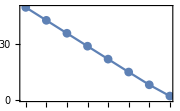

```mathematica
calcNumericDivergence[hilbertComponents]
```

#### SO(7) rep {2,0,0} + singlet with opposite U(1) charges

```mathematica
algebraClass=B;
repDynkinLabels={2,0,0};
rank=Length[repDynkinLabels];
dynkinToIrrep[repDynkinLabels,algebraClass]
char= dynkinToChar[a,repDynkinLabels,algebraClass]
```

27

a_1^2+a_2 a_1+a_3 a_1+a_1/a_2+a_1/a_3+a_1+a_2^2+a_3^2+a_2+a_2 a_3+a_3/a_2+a_3+1/a_2+a_2/a_3+1/(a_2 a_3)+1/a_3+1/a_2^2+1/a_3^2+a_2/a_1+a_3/a_1+1/(a_2 a_1)+1/(a_3 a_1)+1/a_1+1/a_1^2+3

```mathematica
cartanVars=Join[{t},a];
rankTot=Length[repDynkinLabels]+1;
haarU1=1/t;
```

```mathematica
expr=haarU1*haarMeasure[a,algebraClass,rank,type->"Short"] *charToHilbertIntegrand[cartanVars,r,t char+1/t,rankTot]
```

((1-a_1) (1-a_1/a_2) (1-a_2) (1-a_1 a_2) (1-a_1/a_3) (1-a_2/a_3) (1-a_3) (1-a_1 a_3) (1-a_2 a_3))/(a_1 a_2 a_3 t (1-r/t) (1-r t)^3 (1-(r t)/a_1^2) (1-(r t)/a_1) (1-a_1 r t) (1-a_1^2 r t) (1-(r t)/a_2^2) (1-(r t)/a_2) (1-(r t)/(a_1 a_2)) (1-(a_1 r t)/a_2) (1-a_2 r t) (1-(a_2 r t)/a_1) (1-a_1 a_2 r t) (1-a_2^2 r t) (1-(r t)/a_3^2) (1-(r t)/a_3) (1-(r t)/(a_1 a_3)) (1-(a_1 r t)/a_3) (1-(r t)/(a_2 a_3)) (1-(a_2 r t)/a_3) (1-a_3 r t) (1-(a_3 r t)/a_1) (1-a_1 a_3 r t) (1-(a_3 r t)/a_2) (1-a_2 a_3 r t) (1-a_3^2 r t))

```mathematica
{calcTime,hilbertComponents}=calcHilbertIntegral[cartanVars,r,expr,1,rankTot,0,"Branches"]//Timing;
Print["calculation time = ", calcTime, " seconds = ", calcTime/60^2, " hours"];
```

Level = 1

Number of relevant poles = 2

Calculating residue for pole 1/2 in level 1

Calculating residue for pole 2/2 in level 1

Residue for pole 1/2 in level 1 is non-zero, sending to level 2

Level = 2

Number of relevant poles = 7

Calculating residue for pole 1/7 in level 2

Calculating residue for pole 2/7 in level 2

Calculating residue for pole 3/7 in level 2

Calculating residue for pole 4/7 in level 2

Calculating residue for pole 5/7 in level 2

Calculating residue for pole 6/7 in level 2

Calculating residue for pole 7/7 in level 2

Residue for pole 1/7 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 5

Calculating residue for pole 1/5 in level 3

Calculating residue for pole 2/5 in level 3

Calculating residue for pole 3/5 in level 3

Calculating residue for pole 4/5 in level 3

Calculating residue for pole 5/5 in level 3

Residue for pole 1/5 in level 3 is non-zero, sending to level 4

Level = 4

Number of relevant poles = 4

Calculating residue for pole 1/4 in level 4

Calculating residue for pole 2/4 in level 4

Calculating residue for pole 3/4 in level 4

Calculating residue for pole 4/4 in level 4

Residue for pole 2/5 in level 3 is non-zero, sending to level 4

Level = 4

Number of relevant poles = 4

Calculating residue for pole 1/4 in level 4

Calculating residue for pole 2/4 in level 4

Calculating residue for pole 3/4 in level 4

Calculating residue for pole 4/4 in level 4

Residue for pole 3/5 in level 3 is non-zero, sending to level 4

Level = 4

Number of relevant poles = 4

Calculating residue for pole 1/4 in level 4

Calculating residue for pole 2/4 in level 4

Calculating residue for pole 3/4 in level 4

Calculating residue for pole 4/4 in level 4

Residue for pole 4/5 in level 3 is non-zero, sending to level 4

Level = 4

Number of relevant poles = 4

Calculating residue for pole 1/4 in level 4

Calculating residue for pole 2/4 in level 4

Calculating residue for pole 3/4 in level 4

Calculating residue for pole 4/4 in level 4

Residue for pole 5/5 in level 3 is non-zero, sending to level 4

Level = 4

Number of relevant poles = 8

Calculating residue for pole 1/8 in level 4

Calculating residue for pole 2/8 in level 4

Calculating residue for pole 3/8 in level 4

Calculating residue for pole 4/8 in level 4

Calculating residue for pole 5/8 in level 4

Calculating residue for pole 6/8 in level 4

Calculating residue for pole 7/8 in level 4

Calculating residue for pole 8/8 in level 4

Residue for pole 2/7 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 6

Calculating residue for pole 1/6 in level 3

Calculating residue for pole 2/6 in level 3

Calculating residue for pole 3/6 in level 3

Calculating residue for pole 4/6 in level 3

Calculating residue for pole 5/6 in level 3

Calculating residue for pole 6/6 in level 3

Residue for pole 1/6 in level 3 is non-zero, sending to level 4

Level = 4

Number of relevant poles = 4

Calculating residue for pole 1/4 in level 4

Calculating residue for pole 2/4 in level 4

Calculating residue for pole 3/4 in level 4

Calculating residue for pole 4/4 in level 4

Residue for pole 2/6 in level 3 is non-zero, sending to level 4

Level = 4

Number of relevant poles = 4

Calculating residue for pole 1/4 in level 4

Calculating residue for pole 2/4 in level 4

Calculating residue for pole 3/4 in level 4

Calculating residue for pole 4/4 in level 4

Residue for pole 3/6 in level 3 is non-zero, sending to level 4

Level = 4

Number of relevant poles = 4

Calculating residue for pole 1/4 in level 4

Calculating residue for pole 2/4 in level 4

Calculating residue for pole 3/4 in level 4

Calculating residue for pole 4/4 in level 4

Residue for pole 4/6 in level 3 is non-zero, sending to level 4

Level = 4

Number of relevant poles = 5

Calculating residue for pole 1/5 in level 4

Calculating residue for pole 2/5 in level 4

Calculating residue for pole 3/5 in level 4

Calculating residue for pole 4/5 in level 4

Calculating residue for pole 5/5 in level 4

Residue for pole 5/6 in level 3 is non-zero, sending to level 4

Level = 4

Number of relevant poles = 4

Calculating residue for pole 1/4 in level 4

Calculating residue for pole 2/4 in level 4

Calculating residue for pole 3/4 in level 4

Calculating residue for pole 4/4 in level 4

Residue for pole 6/6 in level 3 is non-zero, sending to level 4

Level = 4

Number of relevant poles = 8

Calculating residue for pole 1/8 in level 4

Calculating residue for pole 2/8 in level 4

Calculating residue for pole 3/8 in level 4

Calculating residue for pole 4/8 in level 4

Calculating residue for pole 5/8 in level 4

Calculating residue for pole 6/8 in level 4

Calculating residue for pole 7/8 in level 4

Calculating residue for pole 8/8 in level 4

Residue for pole 3/7 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 6

Calculating residue for pole 1/6 in level 3

Calculating residue for pole 2/6 in level 3

Calculating residue for pole 3/6 in level 3

Calculating residue for pole 4/6 in level 3

Calculating residue for pole 5/6 in level 3

Calculating residue for pole 6/6 in level 3

Residue for pole 1/6 in level 3 is non-zero, sending to level 4

Level = 4

Number of relevant poles = 4

Calculating residue for pole 1/4 in level 4

Calculating residue for pole 2/4 in level 4

Calculating residue for pole 3/4 in level 4

Calculating residue for pole 4/4 in level 4

Residue for pole 2/6 in level 3 is non-zero, sending to level 4

Level = 4

Number of relevant poles = 4

Calculating residue for pole 1/4 in level 4

Calculating residue for pole 2/4 in level 4

Calculating residue for pole 3/4 in level 4

Calculating residue for pole 4/4 in level 4

Residue for pole 3/6 in level 3 is non-zero, sending to level 4

Level = 4

Number of relevant poles = 5

Calculating residue for pole 1/5 in level 4

Calculating residue for pole 2/5 in level 4

Calculating residue for pole 3/5 in level 4

Calculating residue for pole 4/5 in level 4

Calculating residue for pole 5/5 in level 4

Residue for pole 4/6 in level 3 is non-zero, sending to level 4

Level = 4

Number of relevant poles = 4

Calculating residue for pole 1/4 in level 4

Calculating residue for pole 2/4 in level 4

Calculating residue for pole 3/4 in level 4

Calculating residue for pole 4/4 in level 4

Residue for pole 5/6 in level 3 is non-zero, sending to level 4

Level = 4

Number of relevant poles = 4

Calculating residue for pole 1/4 in level 4

Calculating residue for pole 2/4 in level 4

Calculating residue for pole 3/4 in level 4

Calculating residue for pole 4/4 in level 4

Residue for pole 6/6 in level 3 is non-zero, sending to level 4

Level = 4

Number of relevant poles = 8

Calculating residue for pole 1/8 in level 4

Calculating residue for pole 2/8 in level 4

Calculating residue for pole 3/8 in level 4

Calculating residue for pole 4/8 in level 4

Calculating residue for pole 5/8 in level 4

Calculating residue for pole 6/8 in level 4

Calculating residue for pole 7/8 in level 4

Calculating residue for pole 8/8 in level 4

Residue for pole 4/7 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 5

Calculating residue for pole 1/5 in level 3

Calculating residue for pole 2/5 in level 3

Calculating residue for pole 3/5 in level 3

Calculating residue for pole 4/5 in level 3

Calculating residue for pole 5/5 in level 3

Residue for pole 1/5 in level 3 is non-zero, sending to level 4

Level = 4

Number of relevant poles = 4

Calculating residue for pole 1/4 in level 4

Calculating residue for pole 2/4 in level 4

Calculating residue for pole 3/4 in level 4

Calculating residue for pole 4/4 in level 4

Residue for pole 2/5 in level 3 is non-zero, sending to level 4

Level = 4

Number of relevant poles = 4

Calculating residue for pole 1/4 in level 4

Calculating residue for pole 2/4 in level 4

Calculating residue for pole 3/4 in level 4

Calculating residue for pole 4/4 in level 4

Residue for pole 3/5 in level 3 is non-zero, sending to level 4

Level = 4

Number of relevant poles = 4

Calculating residue for pole 1/4 in level 4

Calculating residue for pole 2/4 in level 4

Calculating residue for pole 3/4 in level 4

Calculating residue for pole 4/4 in level 4

Residue for pole 4/5 in level 3 is non-zero, sending to level 4

Level = 4

Number of relevant poles = 3

Calculating residue for pole 1/3 in level 4

Calculating residue for pole 2/3 in level 4

Calculating residue for pole 3/3 in level 4

Residue for pole 5/5 in level 3 is non-zero, sending to level 4

Level = 4

Number of relevant poles = 11

Calculating residue for pole 1/11 in level 4

Calculating residue for pole 2/11 in level 4

Calculating residue for pole 3/11 in level 4

Calculating residue for pole 4/11 in level 4

Calculating residue for pole 5/11 in level 4

Calculating residue for pole 6/11 in level 4

Calculating residue for pole 7/11 in level 4

Calculating residue for pole 8/11 in level 4

Calculating residue for pole 9/11 in level 4

Calculating residue for pole 10/11 in level 4

Calculating residue for pole 11/11 in level 4

Residue for pole 5/7 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 9

Calculating residue for pole 1/9 in level 3

Calculating residue for pole 2/9 in level 3

Calculating residue for pole 3/9 in level 3

Calculating residue for pole 4/9 in level 3

Calculating residue for pole 5/9 in level 3

Calculating residue for pole 6/9 in level 3

Calculating residue for pole 7/9 in level 3

Calculating residue for pole 8/9 in level 3

Calculating residue for pole 9/9 in level 3

Residue for pole 1/9 in level 3 is non-zero, sending to level 4

Level = 4

Number of relevant poles = 4

Calculating residue for pole 1/4 in level 4

Calculating residue for pole 2/4 in level 4

Calculating residue for pole 3/4 in level 4

Calculating residue for pole 4/4 in level 4

Residue for pole 2/9 in level 3 is non-zero, sending to level 4

Level = 4

Number of relevant poles = 4

Calculating residue for pole 1/4 in level 4

Calculating residue for pole 2/4 in level 4

Calculating residue for pole 3/4 in level 4

Calculating residue for pole 4/4 in level 4

Residue for pole 3/9 in level 3 is non-zero, sending to level 4

Level = 4

Number of relevant poles = 4

Calculating residue for pole 1/4 in level 4

Calculating residue for pole 2/4 in level 4

Calculating residue for pole 3/4 in level 4

Calculating residue for pole 4/4 in level 4

Residue for pole 4/9 in level 3 is non-zero, sending to level 4

Level = 4

Number of relevant poles = 5

Calculating residue for pole 1/5 in level 4

Calculating residue for pole 2/5 in level 4

Calculating residue for pole 3/5 in level 4

Calculating residue for pole 4/5 in level 4

Calculating residue for pole 5/5 in level 4

Residue for pole 5/9 in level 3 is non-zero, sending to level 4

Level = 4

Number of relevant poles = 4

Calculating residue for pole 1/4 in level 4

Calculating residue for pole 2/4 in level 4

Calculating residue for pole 3/4 in level 4

Calculating residue for pole 4/4 in level 4

Residue for pole 6/9 in level 3 is non-zero, sending to level 4

Level = 4

Number of relevant poles = 4

Calculating residue for pole 1/4 in level 4

Calculating residue for pole 2/4 in level 4

Calculating residue for pole 3/4 in level 4

Calculating residue for pole 4/4 in level 4

Residue for pole 7/9 in level 3 is non-zero, sending to level 4

Level = 4

Number of relevant poles = 4

Calculating residue for pole 1/4 in level 4

Calculating residue for pole 2/4 in level 4

Calculating residue for pole 3/4 in level 4

Calculating residue for pole 4/4 in level 4

Residue for pole 8/9 in level 3 is non-zero, sending to level 4

Level = 4

Number of relevant poles = 3

Calculating residue for pole 1/3 in level 4

Calculating residue for pole 2/3 in level 4

Calculating residue for pole 3/3 in level 4

Residue for pole 9/9 in level 3 is non-zero, sending to level 4

Level = 4

Number of relevant poles = 11

Calculating residue for pole 1/11 in level 4

Calculating residue for pole 2/11 in level 4

Calculating residue for pole 3/11 in level 4

Calculating residue for pole 4/11 in level 4

Calculating residue for pole 5/11 in level 4

Calculating residue for pole 6/11 in level 4

Calculating residue for pole 7/11 in level 4

Calculating residue for pole 8/11 in level 4

Calculating residue for pole 9/11 in level 4

Calculating residue for pole 10/11 in level 4

Calculating residue for pole 11/11 in level 4

Residue for pole 6/7 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 5

Calculating residue for pole 1/5 in level 3

Calculating residue for pole 2/5 in level 3

Calculating residue for pole 3/5 in level 3

Calculating residue for pole 4/5 in level 3

Calculating residue for pole 5/5 in level 3

Residue for pole 1/5 in level 3 is non-zero, sending to level 4

Level = 4

Number of relevant poles = 4

Calculating residue for pole 1/4 in level 4

Calculating residue for pole 2/4 in level 4

Calculating residue for pole 3/4 in level 4

Calculating residue for pole 4/4 in level 4

Residue for pole 2/5 in level 3 is non-zero, sending to level 4

Level = 4

Number of relevant poles = 4

Calculating residue for pole 1/4 in level 4

Calculating residue for pole 2/4 in level 4

Calculating residue for pole 3/4 in level 4

Calculating residue for pole 4/4 in level 4

Residue for pole 3/5 in level 3 is non-zero, sending to level 4

Level = 4

Number of relevant poles = 4

Calculating residue for pole 1/4 in level 4

Calculating residue for pole 2/4 in level 4

Calculating residue for pole 3/4 in level 4

Calculating residue for pole 4/4 in level 4

Residue for pole 4/5 in level 3 is non-zero, sending to level 4

Level = 4

Number of relevant poles = 3

Calculating residue for pole 1/3 in level 4

Calculating residue for pole 2/3 in level 4

Calculating residue for pole 3/3 in level 4

Residue for pole 5/5 in level 3 is non-zero, sending to level 4

Level = 4

Number of relevant poles = 7

Calculating residue for pole 1/7 in level 4

Calculating residue for pole 2/7 in level 4

Calculating residue for pole 3/7 in level 4

Calculating residue for pole 4/7 in level 4

Calculating residue for pole 5/7 in level 4

Calculating residue for pole 6/7 in level 4

Calculating residue for pole 7/7 in level 4

Residue for pole 7/7 in level 2 is non-zero, sending to level 3

Level = 3

Number of relevant poles = 5

Calculating residue for pole 1/5 in level 3

Calculating residue for pole 2/5 in level 3

Calculating residue for pole 3/5 in level 3

Calculating residue for pole 4/5 in level 3

Calculating residue for pole 5/5 in level 3

Residue for pole 1/5 in level 3 is non-zero, sending to level 4

Level = 4

Number of relevant poles = 8

Calculating residue for pole 1/8 in level 4

Calculating residue for pole 2/8 in level 4

Calculating residue for pole 3/8 in level 4

Calculating residue for pole 4/8 in level 4

Calculating residue for pole 5/8 in level 4

Calculating residue for pole 6/8 in level 4

Calculating residue for pole 7/8 in level 4

Calculating residue for pole 8/8 in level 4

Residue for pole 2/5 in level 3 is non-zero, sending to level 4

Level = 4

Number of relevant poles = 8

Calculating residue for pole 1/8 in level 4

Calculating residue for pole 2/8 in level 4

Calculating residue for pole 3/8 in level 4

Calculating residue for pole 4/8 in level 4

Calculating residue for pole 5/8 in level 4

Calculating residue for pole 6/8 in level 4

Calculating residue for pole 7/8 in level 4

Calculating residue for pole 8/8 in level 4

Residue for pole 3/5 in level 3 is non-zero, sending to level 4

Level = 4

Number of relevant poles = 8

Calculating residue for pole 1/8 in level 4

Calculating residue for pole 2/8 in level 4

Calculating residue for pole 3/8 in level 4

Calculating residue for pole 4/8 in level 4

Calculating residue for pole 5/8 in level 4

Calculating residue for pole 6/8 in level 4

Calculating residue for pole 7/8 in level 4

Calculating residue for pole 8/8 in level 4

Residue for pole 4/5 in level 3 is non-zero, sending to level 4

Level = 4

Number of relevant poles = 7

Calculating residue for pole 1/7 in level 4

Calculating residue for pole 2/7 in level 4

Calculating residue for pole 3/7 in level 4

Calculating residue for pole 4/7 in level 4

Calculating residue for pole 5/7 in level 4

Calculating residue for pole 6/7 in level 4

Calculating residue for pole 7/7 in level 4

Residue for pole 5/5 in level 3 is non-zero, sending to level 4

Level = 4

Number of relevant poles = 11

Calculating residue for pole 1/11 in level 4

Calculating residue for pole 2/11 in level 4

Calculating residue for pole 3/11 in level 4

Calculating residue for pole 4/11 in level 4

Calculating residue for pole 5/11 in level 4

Calculating residue for pole 6/11 in level 4

Calculating residue for pole 7/11 in level 4

Calculating residue for pole 8/11 in level 4

Calculating residue for pole 9/11 in level 4

Calculating residue for pole 10/11 in level 4

Calculating residue for pole 11/11 in level 4

Residue for pole 2/2 in level 1 is zero.

calculation time = 25.0625 seconds = 0.00696181 hours

```mathematica
hilbertComponents//Flatten//Total//Simplify
```

1/((r^2-1)^6 (r^2+1)^3 (r^4+r^2+1)^2 (r^28+r^26+3 r^24+4 r^22+6 r^20+7 r^18+9 r^16+8 r^14+9 r^12+7 r^10+6 r^8+4 r^6+3 r^4+r^2+1))

Numeric divergence degree is -5.91102

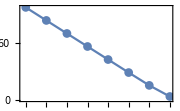

```mathematica
calcNumericDivergence[hilbertComponents]
```